### 加载工具包

```mathematica
Needs["GUIKit`"] (* 获取截图用 *)
Needs["JLink`"] (* 控制鼠标用 *)
ReinstallJava[];
robotclass=JavaNew["java.awt.Robot"];
LoadJavaClass["java.awt.event.InputEvent"];
```

测量游戏四列在屏幕上的坐标

```mathematica
Dynamic[MousePosition[]]
```

```mathematica
x={1450,1495,1735,1775}; (* 尽量拉近左右端提高性能 *)
y0=570; (* 点击点 *)
```

### 探测模块

```mathematica
th=2; (* 经测试，最亮黑块的TotalRGB是 1.7，最暗白块是 2.16 *)
```

```mathematica
xs=x-x⟦1⟧+2;xs⟦4⟧-=2; (* 四探测点在截图中的坐标 *)
(* 用 Module 似乎运行的较慢 *)
checkline[]:=(img=GUIScreenShot[{{x⟦1⟧,x⟦4⟧},{y-4,y}}];
ct=Table[Total@PixelValue[img,{xs⟦i⟧,j}],{i,4},{j,{1,4}}];
Table[ct⟦i,1⟧<th&&ct⟦i,1⟧==ct⟦i,2⟧,{i,4}]
) (* 跨一段距离是为了避免误把黑线判成黑块 *)
checklineC[]:=(ch=checkline[];If[ch⟦1⟧,click[1],If[ch⟦2⟧,click[2],If[ch⟦3⟧,click[3],If[ch⟦4⟧,click[4]]]]];
)
```

### 测鼠标点击事件的延迟

```mathematica
click[i_]:=(robotclass@mouseMove[x⟦i⟧,y0];robotclass@mousePress[16];robotclass@mouseRelease[16];)
```

```mathematica
Do[click[Mod[i,4,1]],{i,4000}]//Timing
```

{2.64063,Null}

屏幕外实测时间为 10.2 s，故单次点击的延迟为

```mathematica
10.2/4000
```

0.00255

（此外安卓模拟器翻译鼠标点击事件似乎也有延迟）

### 测 t=0 时的 delay 所允许的像素取值区间

调 y0=y+Δ 使游戏刚好死于 n=450

```mathematica
n=1;y=570;y0=y+260; (* 开局延迟最大只能这么大*)
While[n<450,checklineC[];y0--;y--;n++;If[n==300,y0=y+386]];
While[n<500,checklineC[];n++]
```

```mathematica
Dynamic[{n,y,y0}]
```

```mathematica
n=1;y=600;y0=y-16; 
While[n<450,checklineC[];y0--;y--;n++];
While[n<500,checklineC[];n++]
```

测得下限为 y0=y-15，上限为  y0=y+385

```mathematica
(385-15)/2
```

185

### 调后退速率使存活时间最长

```mathematica
n=1;y=570;y0=y+185;
(* 开局先把阵线尽量往前推… *)
While[n<460,checklineC[];y0--;y--;n++]
(* 中盘 *)
While[n<4000,checklineC[];n++;
(* 随着游戏 bps 线性加快，触点应匀速后撤 *)
If[Mod[n,50]==0,y0++]]
```

```mathematica
Dynamic[{n,y,y0}]
```

If[Mod[n,4]==0,y0++] 死于 n=1300，bps=8.1/s
If[Mod[n,10]==0,y0++] 死于 n=2550，bps=12.3/s
If[Mod[n,20]==0,y0++] 死于 n=2850，bps=13.5/s
If[Mod[n,50]==0,y0++] 死于 n=2050，bps=10.6/s
y0 不变 死于 n=1790，bps=9.8/s

```mathematica
SetOptions[Plot,Frame->True];
```

```mathematica
f[mod_]:=(s-450)/mod+185;
```

```mathematica
data={{450,-15},{450,385},{s,f[4]}/.s->1300,{s,f[10]}/.s->2550,{s,f[20]}/.s->2850,{s,f[50]}/.s->2050,{1790,185}}
```

{{450,-15},{450,385},{1300,795/2},{2550,395},{2850,305},{2050,217},{1790,185}}

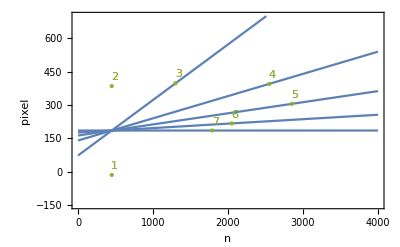

```mathematica
Show[
Plot[{f[4],f[10],f[20],f[50],185},{s,0,4000},PlotRange->{-150,700},FrameLabel->{"n","pixel"},PlotStyle->RGBColor[0.368417, 0.506779, 0.709798],
Epilog->{RGBColor[0.560181, 0.691569, 0.194885],PointSize@Large,Point[data]}],
ListPlot[Table[{data⟦i⟧+40},{i,Length@data}],PlotMarkers->ToString/@Range@Length@data,PlotStyle->RGBColor[0.560181, 0.691569, 0.194885]]
]
```

```mathematica
line1=LinearModelFit[data⟦{1,7,6,5}⟧,s,s]//Normal
```

-68.0201+0.135025 s

```mathematica
line2=LinearModelFit[data⟦{2,3,4}⟧,s,s]//Normal
```

386.398+0.00425691 s

```mathematica
Solve[line1==line2,s]
```

{{s→3474.99}}

```mathematica
pos={s,line1}/.s->3475
```

{3475,401.193}

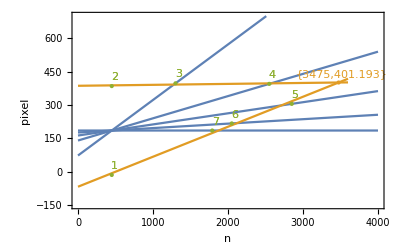

```mathematica
Show[%211,Plot[{line1,line2},{s,0,3600},PlotStyle->RGBColor[0.880722, 0.611041, 0.142051]],
Graphics[{RGBColor[0.880722, 0.611041, 0.142051],PointSize@Large,Point[pos],Text[pos,pos+40]}]]
```

```mathematica
1/((401.2-185)/(3475-450))
```

13.9917

### 所以将 mod 数设成 14 即可达到麦酱的性能极限（预计上限成绩为 n=3475）

```mathematica
n=1;y=570;y0=y+185;
(* 开局先把阵线尽量往前推 *)
While[n<460,checklineC[];y0--;y--;n++]
(* 中盘 *)
While[n<4000,checklineC[];n++;
(* 随着游戏 bps 线性加快，触点应匀速后撤 *)
If[Mod[n,14]==0,y0++]]
```

$Aborted

```mathematica
Dynamic[{n,y,y0}]
```